# Creating a densely-connected deep neural network

## Deep neural networks

Deep leaning is a branch of machine learning.  It is loosely based on the neural structure of the brain, representing layers of connected neurons.
The image below, taken from Wikimedia Common shows a diagram of a neuron.  The cell body is on the left.  It has many dendrites stemming from it.  A long axon terminating in many branches flows from the cell body.  The dendrites connect to the axon terminal ends of many other neurons.  Electrical impulse flow from the dendrites, along the axon.  The impulse is transmitted to dendrites of other neuron on a selected basis.

A linear regression model can also be viewed as a network of neurons.

In the image above, the first (vertical layer), represented as three nodes, is the input layer.  Each node carries the value of a variable.  In a spreadsheet file, this might be a row with three entries.  Each entry is in its own column, with each column (header) being one of the three variables.  In machine learning these variables are referred to as feature variables.  The fourth column in this scenario, would be the target variable.  The aim is to use the values of the three feature variable to predict the value of the target variable.

The second layer above represents a hidden layer of three nodes.  A weight, β_i, is multiplied by each feature variable value.  A bias term is added to the sum of  each of the product.  This results in a predicted target value, (ŷ)_i.  This algorithm is termed forward propagation.  During the first run of this forward propagation, random values are selected for the weights and the bias.

The predicted value might be different from the actual value, y_i.  Depending on the type of the target variable, there are a number of ways of calculating the difference between the predicted and the actual value.  This difference is termed the loss function.

All of the sample (rows) in a dataset go through the same algorithm outlined above (forward propagation).  The losses are combined in a cost function.  The cost function is a multivariable function with all the weights and bias value forming the unknowns.

By a process termed backpropagation, the weights  and bias can be updated by gradient descent aimed as minimizing the cost function.  This minimization is done through the calculation of the partial derivative of the cost function with respect to each of the unknowns, a single variable simplification of which is demonstrated below.

Gradient descent updates the weight and bias values by subtracting the product of a learning rate value and the partial derivative the previous value from the previous value.

This process (of forward propagation and backpropagation algorithms) repeats through many epochs until (hopefully) the values of the unknowns converge to a minimum for the cost function.

A densely-connected deep neural network differs from a linear regression problem by the addition of activation functions for every node in a layer.  This introduces non-linear decision boundaries.  Every node in a layer is also connected to every other node in a prior layer.  The diagram below shows shows an input layer representing 10 feature variables.  The first hidden layer similarly has 10 nodes and a bias node.  This is repeated for a second hidden layer.  The output layer has two nodes.  The total number of unknowns (parameters) in the cost function is (10×10+10)+(10×10+10)+(10×2+2)=242.  This represents a cost function in 242 dimensions.

The code and description below imports data from a spreadsheet file and creates a deep neural network as a demonstration of the process.  A target variable exists making this a supervised learning problem.  Since the target variable is binary, representing a class, this is further classified as a classification problem.

## Data import

The current notebook directory can be set as the default directory.  This makes importing files from this directory or its subdirectories easier.

```mathematica
SetDirectory[NotebookDirectory[]];
```

Importing a simulated dataset with 29963 samples, 13 feature variables, and a binary target variable encoded as 0 and 1.   There are no column names in the original spreadsheet file.  The dataset contains much overlapping between the target classes making for a very difficult learning.

```mathematica
dataImport=Import["DCDNNData.csv"];
```

The Dimension[] function can be used to verify the number of rows and columns.

```mathematica
Dimensions[dataImport]
```

{29963,13}

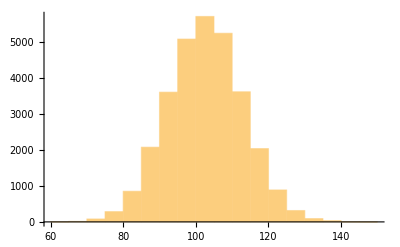
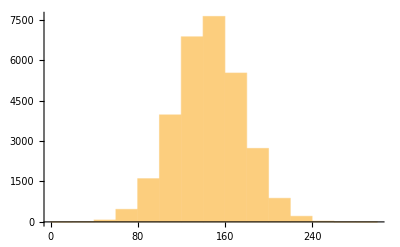
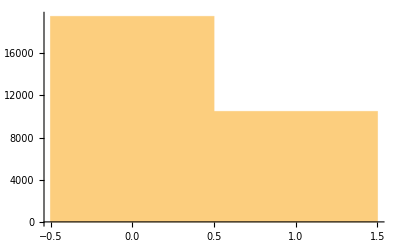
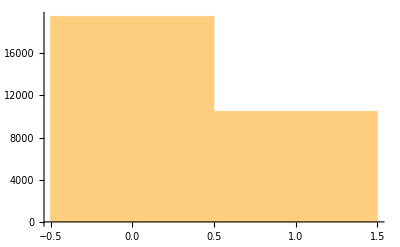
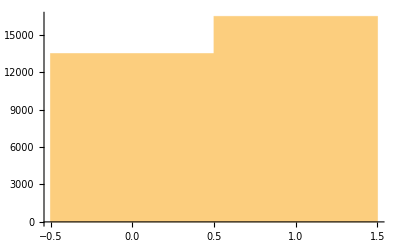
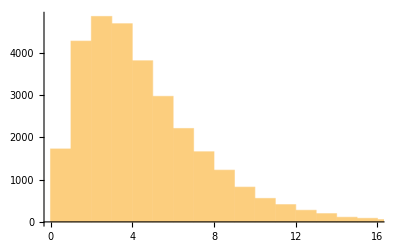
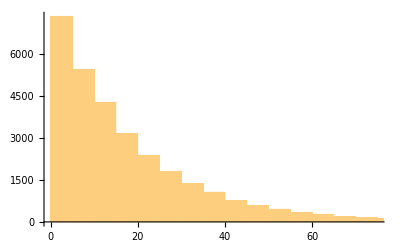
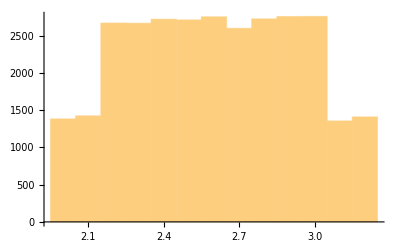

```mathematica
Table[Histogram[dataImport⟦;;,i⟧],{i,12}]
```

## Splitting the data into training and test sets

Setting the number of rows.

```mathematica
n=Length[dataImport]
```

29963

Creating a variable to hold 90% of the data.

```mathematica
trainN=Floor[0.9*n]
```

26966

Given a list (first argument), the TakeDrop[] function selects the first n elements (second argument) and returns it as the first sublist in a list object.  The remainder is placed in a second sublist.  These two sublists can be individually named as separate objects.  By adding the RandomSample[] function, a random selection of rows of similar size, n, is taken as first sublist and the complement is stored in the second sublist.

```mathematica
RandomSeed[123];
{dataTrain,dataTest}=TakeDrop[RandomSample@dataImport,trainN];
Dimensions[dataTrain]
Dimensions[dataTest]
```

{26966,13}

{2997,13}

Create variables to separately hold the feature variables and the target variable for each of the training and test sets.

```mathematica
xTrain=dataTrain⟦All,1;;12⟧;
yTrain=dataTrain⟦All,13⟧;
xTest=dataTest⟦All,1;;12⟧;
yTest=dataTest⟦All,13⟧;
```

Using a histogram to verify the distribution of the target classes.

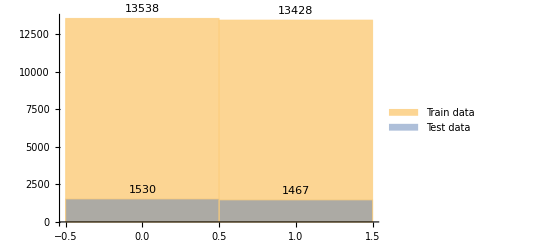

```mathematica
Histogram[{yTrain,yTest},ChartLegends->{"Train data","Test data"},LabelingFunction->Above]
```

## Manipulating the data

Data manipulation starts with transforming the scale of each of the feature variables.  One such method is standardization, shown in equation (1) for the mean and standard deviation for each specific variable (column).

x_i=(x_i-x̄)/σ

The mean of each column is shown below

```mathematica
Mean[xTrain]//N
```

{102.548,145.129,0.350145,0.350738,0.550063,4.49269,17.9189,2.60163,0.349922,9.89461,1010.83,145.339}

The standard deviation for each column is also shown.

```mathematica
StandardDeviation[xTrain]//N
```

{10.2736,30.782,0.477024,0.47721,0.497497,3.02938,18.0817,0.333125,0.476954,9.07562,205.712,32.2848}

The Map[] function maps a function to a list object.  The latter must be transposed (as the function maps over rows and not columns) and the result transposed again to recreate the original data dimensions.  The code below shows a mean of 0 and a standard deviation of 1 for each of the variables.

```mathematica
xTrainStandardized=Transpose@Map[Standardize,Transpose[xTrain]];
Mean[xTrainStandardized]
StandardDeviation[xTrainStandardized]
```

{-4.80089×10^-16,3.92477×10^-16,0,0,0,1.60732×10^-16,-1.23843×10^-16,-4.43727×10^-16,0,1.16202×10^-16,-6.18029×10^-16,-1.27532×10^-16}

{1.,1.,1,1,1,1.,1.,1.,1,1.,1.,1.}

The same transformation must occur for the test data.  However, it is important that the mean and standard deviation of the training data variables be used for the transformation.

```mathematica
xTestStandardized=Transpose@Table[(xTest[[All,i]]-Mean[xTrain][[i]])/StandardDeviation[xTrain][[i]],{i,12}];
```

The mean and standard deviation of the test data variables will not quite be 0 and 1.

```mathematica
Mean[xTestStandardized]//N
StandardDeviation[xTestStandardized]//N
```

{-0.009081,0.00645104,-0.0114598,-0.0217884,-0.00773907,-0.0056167,-0.0121214,-0.0145026,0.00719405,0.019251,-0.0227056,-0.0140159}

{0.970052,0.998052,0.996475,0.99307,1.0009,0.992126,0.998255,1.00895,1.00238,1.02714,0.996945,0.994819}

A variable called train is created to hold a list of the feature variables and each individual sample target class using the Table[] function to iterate over each sample.

```mathematica
train=Table[xTrainStandardized⟦i,All⟧->yTrain⟦i⟧,{i,trainN}];
Dimensions[train]
train⟦;;1⟧ //N (*Show first sample*)
```

{26966}

{{-1.74702,-0.377797,-0.734019,-0.734976,-1.10566,2.47817,-0.570681,-0.605263,-0.73366,-0.583388,-0.649131,0.729784}→0.}

The same is done for the test set.

```mathematica
test=Table[xTestStandardized⟦i,All⟧->yTest⟦i⟧,{i,Length[yTest]}];
Dimensions[test]
test⟦;;1⟧//N
```

{2997}

{{-1.02673,-0.215364,-0.734019,-0.734976,-1.10566,-0.360698,3.69882,-1.20564,-0.73366,-0.109591,2.37208,0.605887}→0.}

## Creating the neural network

A decoder is created to specify the two classes in the target variable.

```mathematica
dec=NetDecoder[{"Class",{0,1}}]
```

NetDecoder[<>]

Examples of two networks are shown below.

```mathematica
SeedRandom[123]
netOne=NetInitialize[NetChain[{5,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->12],Method->{"Random","Weights"->0.01,"Biases"->0}]
netTwo=NetInitialize[NetChain[{5,Ramp,5,Ramp,2,SoftmaxLayer[]},"Output"->dec,"Input"->12],Method->{"Xavier","FactorType"->"Mean","Distribution"->"Uniform"}]
```

NetChain[<>]

NetChain[<>]

```mathematica
NetExtract[netOne,{1,"Weights"}]
```

{{0.0124155,-0.00174105,0.00332349,-0.00080418,-0.0151301,0.00321184,-0.017771,0.0155398,0.0023342,-0.0127836,-0.01703,-0.0177439},{0.0134985,0.0085923,0.00397305,0.00324943,0.0141971,-0.00796722,0.0152614,0.0110264,-0.0100837,0.00701713,-0.000952603,0.00220404},{-0.00283875,0.020164,-0.00472625,-0.00882728,-0.0168131,0.000866731,-0.0102118,-0.00326107,-0.00745353,-0.00951678,-0.00372535,-0.0126804},{0.00231089,-0.00159592,-0.00356508,-0.00387673,-0.0125969,0.00533063,-0.0105669,0.00113915,0.018624,-0.00436825,-0.0247961,0.000582389},{0.0118078,0.000918188,0.0105407,0.00566773,-0.00839401,-0.00927818,-0.00570327,-0.0099605,-0.00800916,0.00486881,0.000252674,-0.0010136}}

The initial random weight values can be shown.

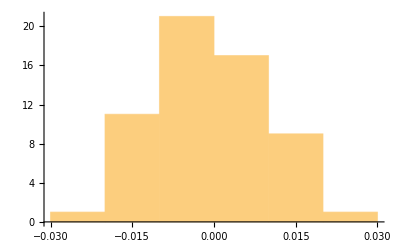

```mathematica
Histogram[Flatten[NetExtract[netOne,{1,"Weights"}]],{0.01}]
```

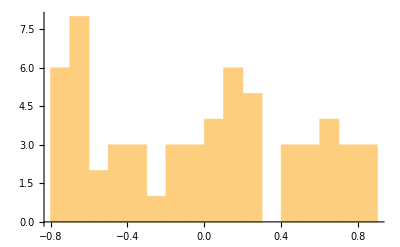

```mathematica
Histogram[Flatten[NetExtract[netTwo,{1,"Weights"}]],{0.1}]
```

Examples are left in comments below (**).

```mathematica
(*trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"GPU",LossFunction->CrossEntropyLossLayer["Binary"],Method->{"ADAM","Beta1"->0.9,"L2Regularization"->0.1,"LearningRate"->0.0003},MaxTrainingRounds->25]*)
(*trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"GPU",MaxTrainingRounds->25]*)
trained=NetTrain[netOne,train,BatchSize->256,ValidationSet->test,TargetDevice->"GPU",Method->"SGD",MaxTrainingRounds->25]
```

NetChain[<>]

The first  sample row is passed as an argument to show the predicted target value.

```mathematica
trained[xTestStandardized[[1]]]
```

0

A classifier measurements object can be created.

```mathematica
c=ClassifierMeasurements[trained,test]
```

ClassifierMeasurementsObject[…]

A list of properties for this object can be extracted.

```mathematica
c["Properties"]
```

{Accuracy,AccuracyBaseline,AccuracyRejectionPlot,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,EvaluationTime,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeRate,FalsePositiveExamples,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictedValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,Report,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TruePositiveExamples,WorstClassifiedExamples}

Showing the accuracy property.

```mathematica
c["Accuracy"]
```

0.709376

A confusion matrix plot shows the errors and correct predictions.

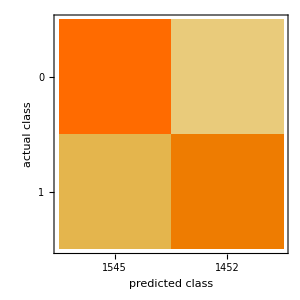

```mathematica
c["ConfusionMatrixPlot"]
```

More of the properties are explored below.

```mathematica
c["Report"]
```

Classifier Measurements
Number of test examples | 2997
Accuracy | 70.9 % ± 0.83 %
Accuracy baseline | 51.1 % ± 0.91 %
Geometric mean of probabilities | 0.574 ± 0.0044
Mean cross entropy | 0.556 ± 0.0077
Single evaluation time | 1.64 ms/example
Batch evaluation speed | 19. examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
c["AreaUnderROCCurve"]
```

<|0→0.785813,1→0.785836|>

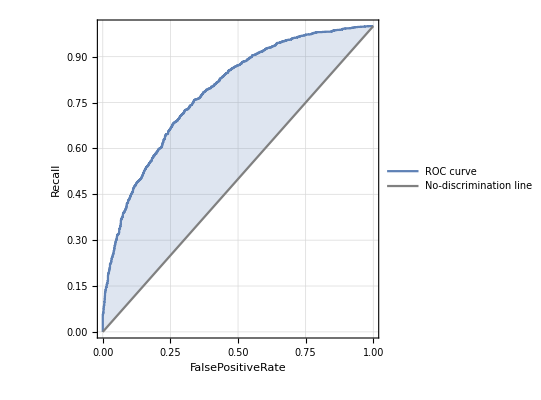
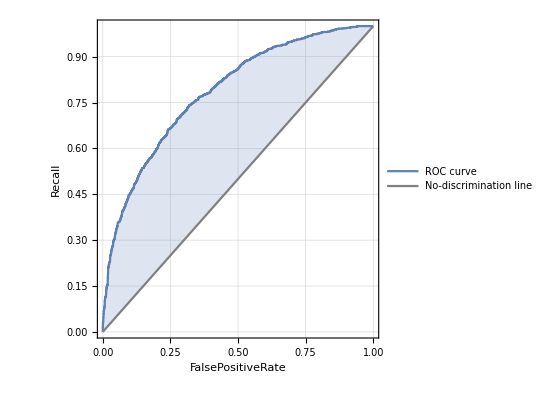
<|0→-Graphics-,1→-Graphics-|>

```mathematica
c["ROCCurve"]
```

```mathematica
c["ClassMeanCrossEntropy"]
```

<|0→0.542206,1→0.569446|>